## G8, G4, and G2

The basic big matrix is
	(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | p4 | -p3 | p6 | -p5 | -p8 | p7
-p3 | -p4 | p1 | p2 | p7 | p8 | -p5 | -p6
-p4 | p3 | -p2 | p1 | p8 | -p7 | p6 | -p5
-p5 | -p6 | -p7 | -p8 | p1 | p2 | p3 | p4
-p6 | p5 | -p8 | p7 | -p2 | p1 | -p4 | p3
-p7 | p8 | p5 | -p6 | -p3 | p4 | p1 | -p2
-p8 | -p7 | p6 | p5 | -p4 | -p3 | p2 | p1).
You can get the little guys by grabbing chunks. Of course this needs to be normalized by

```mathematica
Clear[G8]
G8[{p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_}]:=Module[{},
({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}})]
G4[{p1_,p2_,p3_,p4_}]:=Module[{},
({{p1, p2, p3, p4}, {-p2, p1, p4, -p3}, {-p3, -p4, p1, p2}, {-p4, p3, -p2, p1}})]
G2[{p1_,p2_}]:=Module[{},
({{p1, p2}, {-p2, p1}})]
{p2,p4,p8}=Map[Normalize[RandomReal[{-1,1},#]]&,{2,4,8}];
{Q2,Q4,Q8}={G2[p2],G4[p4],G8[p8]};
Map[Norm,
 {Q2ᵀ.Q2-IdentityMatrix[2],
Q4ᵀ.Q4-IdentityMatrix[4],
Q8ᵀ.Q8-IdentityMatrix[8]}]
```

{2.22045×10^-16,2.95413×10^-17,2.62872×10^-16}

```mathematica
Clear[p1,p2,p3,p4]
A=RandomReal[{-1,1},{4,4}];
G=G4[{p1,p2,p3,p4}];
NewA=G.A.Gᵀ;
Simplify[NewA⟦4,1⟧]
```

## Optimization

We can make any specific output entry of A_(k+1)=G.A.Gᵀ as “big” (ignoring ± signs) as possible.  This is a single dominant eigenvector computation for a symmetric matrix. This is cheaply approximable and even a full accuracy computation is significantly cheaper than the original eigenvalue problem.

We can make any weighted sum of specific output entries as “big” (ignoring ± signs) as possible.  This is still a single dominant eigenvector computation for a symmetric matrix: cheaply and easily approximable.

The Jacobi algorithm for the symmetric (A=Aᵀ ) eigenvalue problem consistently zeros of diagonal matrix elements using G_2 to make the diagonal elements big.

There is no analog of the Jacobi algorithm for the non-symmetric (A≠Aᵀ ) eigenvalue problem.

The plan is to create a G_4 and G_8 analog of the Jacobi algorithm to compute the eigenvalues of symmetric A i.e. A=Aᵀ by making a weighted average of the diagonal elements big

Compute the eigenvalues of a 4x4 with A=Aᵀ.

Compare to Jacobi with various pivot selection strategies.

Compute the eigenvalues of a 8x8 with A=Aᵀ.

Compare to Jacobi with various pivot selection strategies.

Embed the G_4 algorithm in an n×n computation.

Compare to Jacobi with various pivot selection strategies.

Embed the G_8 algorithm in an n×n computation

Compare to Jacobi with various pivot selection strategies.

The plan is to create a Jacobi like  (G_4 and G_8 based) algorithm to compute the eigenvalues of non-symmetric A i.e. A≠Aᵀ by making a weighted average of the upper triangular elements big

Compute the eigenvalues of a 4x4 with A≠Aᵀ.

Try to understand the convergence.

Compute the eigenvalues of a 8x8 with A≠Aᵀ.

Try to understand the convergence.

Embed the G_4 algorithm in an n×n computation.

Try to understand the convergence.

Embed the G_8 algorithm in an n×n computation

Try to understand the convergence.

### Formula i=j=1.

Easy enough to do for i=j=1 the answer is A_sym=0.5(A+Aᵀ)

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={1,1};
B1=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B1]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B1S=B1/.SymSub]
```

(a[1,1] | 1/2 (a[1,2]+a[2,1]) | 1/2 (a[1,3]+a[3,1]) | 1/2 (a[1,4]+a[4,1])
1/2 (a[1,2]+a[2,1]) | a[2,2] | 1/2 (a[2,3]+a[3,2]) | 1/2 (a[2,4]+a[4,2])
1/2 (a[1,3]+a[3,1]) | 1/2 (a[2,3]+a[3,2]) | a[3,3] | 1/2 (a[3,4]+a[4,3])
1/2 (a[1,4]+a[4,1]) | 1/2 (a[2,4]+a[4,2]) | 1/2 (a[3,4]+a[4,3]) | a[4,4])

(a[1,1] | a[1,2] | a[1,3] | a[1,4]
a[1,2] | a[2,2] | a[2,3] | a[2,4]
a[1,3] | a[2,3] | a[3,3] | a[3,4]
a[1,4] | a[2,4] | a[3,4] | a[4,4])

### Formula i=j=2.

Easy enough to do for i=j=2.

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={2,2};
B2=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B2]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B2S=B2/.SymSub]
```

(a[2,2] | 1/2 (-a[1,2]-a[2,1]) | 1/2 (-a[2,4]-a[4,2]) | 1/2 (a[2,3]+a[3,2])
1/2 (-a[1,2]-a[2,1]) | a[1,1] | 1/2 (a[1,4]+a[4,1]) | 1/2 (-a[1,3]-a[3,1])
1/2 (-a[2,4]-a[4,2]) | 1/2 (a[1,4]+a[4,1]) | a[4,4] | 1/2 (-a[3,4]-a[4,3])
1/2 (a[2,3]+a[3,2]) | 1/2 (-a[1,3]-a[3,1]) | 1/2 (-a[3,4]-a[4,3]) | a[3,3])

(a[2,2] | -a[1,2] | -a[2,4] | a[2,3]
-a[1,2] | a[1,1] | a[1,4] | -a[1,3]
-a[2,4] | a[1,4] | a[4,4] | -a[3,4]
a[2,3] | -a[1,3] | -a[3,4] | a[3,3])

### Formula i=j=3.

Easy enough to do for i=j=3

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={3,3};
B3=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B3]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B3S=B3/.SymSub]
```

(a[3,3] | 1/2 (a[3,4]+a[4,3]) | 1/2 (-a[1,3]-a[3,1]) | 1/2 (-a[2,3]-a[3,2])
1/2 (a[3,4]+a[4,3]) | a[4,4] | 1/2 (-a[1,4]-a[4,1]) | 1/2 (-a[2,4]-a[4,2])
1/2 (-a[1,3]-a[3,1]) | 1/2 (-a[1,4]-a[4,1]) | a[1,1] | 1/2 (a[1,2]+a[2,1])
1/2 (-a[2,3]-a[3,2]) | 1/2 (-a[2,4]-a[4,2]) | 1/2 (a[1,2]+a[2,1]) | a[2,2])

(a[3,3] | a[3,4] | -a[1,3] | -a[2,3]
a[3,4] | a[4,4] | -a[1,4] | -a[2,4]
-a[1,3] | -a[1,4] | a[1,1] | a[1,2]
-a[2,3] | -a[2,4] | a[1,2] | a[2,2])

### Formula i=j=4.

Easy enough to do for i=j=4

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={4,4};
B4=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B4]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B4S=B4/.SymSub]
```

(a[4,4] | 1/2 (-a[3,4]-a[4,3]) | 1/2 (a[2,4]+a[4,2]) | 1/2 (-a[1,4]-a[4,1])
1/2 (-a[3,4]-a[4,3]) | a[3,3] | 1/2 (-a[2,3]-a[3,2]) | 1/2 (a[1,3]+a[3,1])
1/2 (a[2,4]+a[4,2]) | 1/2 (-a[2,3]-a[3,2]) | a[2,2] | 1/2 (-a[1,2]-a[2,1])
1/2 (-a[1,4]-a[4,1]) | 1/2 (a[1,3]+a[3,1]) | 1/2 (-a[1,2]-a[2,1]) | a[1,1])

(a[4,4] | -a[3,4] | a[2,4] | -a[1,4]
-a[3,4] | a[3,3] | -a[2,3] | a[1,3]
a[2,4] | -a[2,3] | a[2,2] | -a[1,2]
-a[1,4] | a[1,3] | -a[1,2] | a[1,1])

### Formula ∑_(i=1)^4 α_i (Â)_(i,i).

Easy enough to add them up. This is NOT efficient but we just want to know how well it works.

#### If you want to see how I avoided some typing

```mathematica
Clear[A]
Quiet[α1 {{a[1,1],a[1,2],a[1,3],a[1,4]},{a[1,2],a[2,2],a[2,3],a[2,4]},{a[1,3],a[2,3],a[3,3],a[3,4]},{a[1,4],a[2,4],a[3,4],a[4,4]}}+
α2 {{a[2,2],-a[1,2],-a[2,4],a[2,3]},{-a[1,2],a[1,1],a[1,4],-a[1,3]},{-a[2,4],a[1,4],a[4,4],-a[3,4]},{a[2,3],-a[1,3],-a[3,4],a[3,3]}}+
α3 {{a[3,3],a[3,4],-a[1,3],-a[2,3]},{a[3,4],a[4,4],-a[1,4],-a[2,4]},{-a[1,3],-a[1,4],a[1,1],a[1,2]},{-a[2,3],-a[2,4],a[1,2],a[2,2]}}+
α4{{a[4,4],-a[3,4],a[2,4],-a[1,4]},{-a[3,4],a[3,3],-a[2,3],a[1,3]},{a[2,4],-a[2,3],a[2,2],-a[1,2]},{-a[1,4],a[1,3],-a[1,2],a[1,1]}}/.{a[i_,j_]:>A⟦i,j⟧}]
```

#### Continued

```mathematica
BDiaS[{α1_,α2_,α3_,α4_},A_]:={{α1 A⟦1,1⟧+α2 A⟦2,2⟧+α3 A⟦3,3⟧+α4 A⟦4,4⟧,α1 A⟦1,2⟧-α2 A⟦1,2⟧+α3 A⟦3,4⟧-α4 A⟦3,4⟧,α1 A⟦1,3⟧-α3 A⟦1,3⟧-α2 A⟦2,4⟧+α4 A⟦2,4⟧,α1 A⟦1,4⟧-α4 A⟦1,4⟧+α2 A⟦2,3⟧-α3 A⟦2,3⟧},{α1 A⟦1,2⟧-α2 A⟦1,2⟧+α3 A⟦3,4⟧-α4 A⟦3,4⟧,α2 A⟦1,1⟧+α1 A⟦2,2⟧+α4 A⟦3,3⟧+α3 A⟦4,4⟧,α2 A⟦1,4⟧-α3 A⟦1,4⟧+α1 A⟦2,3⟧-α4 A⟦2,3⟧,-α2 A⟦1,3⟧+α4 A⟦1,3⟧+α1 A⟦2,4⟧-α3 A⟦2,4⟧},{α1 A⟦1,3⟧-α3 A⟦1,3⟧-α2 A⟦2,4⟧+α4 A⟦2,4⟧,α2 A⟦1,4⟧-α3 A⟦1,4⟧+α1 A⟦2,3⟧-α4 A⟦2,3⟧,α3 A⟦1,1⟧+α4 A⟦2,2⟧+α1 A⟦3,3⟧+α2 A⟦4,4⟧,α3 A⟦1,2⟧-α4 A⟦1,2⟧+α1 A⟦3,4⟧-α2 A⟦3,4⟧},{α1 A⟦1,4⟧-α4 A⟦1,4⟧+α2 A⟦2,3⟧-α3 A⟦2,3⟧,-α2 A⟦1,3⟧+α4 A⟦1,3⟧+α1 A⟦2,4⟧-α3 A⟦2,4⟧,α3 A⟦1,2⟧-α4 A⟦1,2⟧+α1 A⟦3,4⟧-α2 A⟦3,4⟧,α4 A⟦1,1⟧+α3 A⟦2,2⟧+α2 A⟦3,3⟧+α1 A⟦4,4⟧}}
```

I am going to test this a bit.  Essentially by definition the maximum of a symmetric quadratic form p.B.p for ||p||=1  is the largest eigenvalue of B.
 Essentially by definition the minimum of a symmetric quadratic form p.B.p for ||p||=1  is the smallest eigenvalue of B.  Almost all eigen solvers return the eigenvector with the biggest absolute value eigenvalue first.

```mathematica
n=4;
A0=RandomReal[{-1,1},{n,n}]; A0=A0+A0ᵀ;
α={-10.0,1.2,3.4,-0.9};
B = BDiaS[α,A0];
Eigenvalues[B]
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A1=Q.A0.Qᵀ;
Diagonal[A1].α
TabView[{
"pic"->MatrixPlot[A1],
"vals"->MatrixForm[A1]
}]
```

{22.0103,-20.0179,5.87786,-3.63814}

22.0103

12

The actual algorithm uses the Diagonal of the input matrix as the weights.  One step of this should get the diagonals close to the eigenvalues if I use the eigenvalues as weights.  Yes this is cheating a bit.

```mathematica
n=4;
A0=RandomReal[{-1,1},{n,n}]; A0=A0+A0ᵀ;
α=Diagonal[A0];
B = BDiaS[α,A0];
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A1=Q.A0.Qᵀ;
{Diagonal[A1].α,Eigenvalues[B]};
vars=Array[p,4];
Q=G4[vars];
FNormSqA0=Norm[A0,"Frobenius"]^2;
(Diagonal[A0].Diagonal[A0])/FNormSqA0
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]}
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]}
(Diagonal[A1].Diagonal[A1])/FNormSqA0
```

0.239793

{{0.276165,{p[1]→0.480105,p[2]→0.132423,p[3]→0.0531683,p[4]→-0.865527}},{5.80788,{p[1]→0.780493,p[2]→0.356978,p[3]→0.132903,p[4]→0.495717}}}

{{0.276165,{p[1]→3.19543×10^-17,p[2]→-0.0733555,p[3]→0.396928,p[4]→0.914914}},{5.80788,{p[1]→1.,p[2]→5.12992×10^-16,p[3]→-5.11464×10^-17,p[4]→5.50054×10^-17}}}

0.676128

```mathematica
n=4;
A0=RandomReal[{-1,1},{n,n}]; A0=A0+A0ᵀ;
α=Eigenvalues[A0];
B = BDiaS[α,A0];
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A1=Q.A0.Qᵀ;
{Diagonal[A1].α,Eigenvalues[B]};
vars=Array[p,4];
Q=G4[vars];
FNormSqA0=Norm[A0,"Frobenius"]^2;
(Diagonal[A0].Diagonal[A0])/FNormSqA0
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]};
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]};
(Diagonal[A1].Diagonal[A1])/FNormSqA0
```

0.413896

0.230238

```mathematica
Diagonal[A0].α
Diagonal[A1].α
```

2.42451

4.17418

```mathematica
FindMinimum[Diagonal[
TabView[{
"pic"->MatrixPlot[A1],
"vals"->MatrixForm[A1]
}];
Map[Eigenvalues,{A0,A1}]ᵀ
```

{9.01436,{9.01436,2.69122,1.07849,-0.819528}}

{{3.12777,3.12777},{1.05501,1.05501},{-0.547194,-0.547194},{-0.176606,-0.176606}}

```mathematica
MatrixForm[A1]
```

(-0.0904343 | -0.180367 | -0.306573 | -0.663712
-0.180367 | -2.46124 | -0.378566 | -0.998966
-0.306573 | -0.378566 | 1.20317 | 0.134659
-0.663712 | -0.998966 | 0.134659 | -1.37352)

```mathematica
A=Array[a,{4,4}];
Sub=Flatten[
Table[
a[i,j]->a[j,i],
{i,1,4},{j,1,i-1}]];
A=A/.Sub;
Hmm=Q.A.Qᵀ;
Simplify[Hmm⟦1,1⟧]==a[1,1]
Simplify[Hmm⟦2,2⟧]==a[2,2]
```

a[1,1] p[1]^2+2 a[1,2] p[1] p[2]+a[2,2] p[2]^2+2 a[1,3] p[1] p[3]+2 a[2,3] p[2] p[3]+a[3,3] p[3]^2+2 a[1,4] p[1] p[4]+2 a[2,4] p[2] p[4]+2 a[3,4] p[3] p[4]+a[4,4] p[4]^2==a[1,1]

a[2,2] p[1]^2-2 a[1,2] p[1] p[2]+a[1,1] p[2]^2-2 a[2,4] p[1] p[3]+2 a[1,4] p[2] p[3]+a[4,4] p[3]^2+2 a[2,3] p[1] p[4]-2 a[1,3] p[2] p[4]-2 a[3,4] p[3] p[4]+a[3,3] p[4]^2==a[2,2]

```mathematica
Simplify[Simplify[Hmm⟦1,1⟧+Hmm⟦2,2⟧+Hmm⟦3,3⟧+Hmm⟦4,4⟧]/.p[1]^2+p[2]^2+p[3]^2+p[4]^2->1]
```

1+a[1,1]+a[2,2]+a[3,3] p[1]^2+a[4,4] p[1]^2+a[3,3] p[2]^2+a[4,4] p[2]^2+a[3,3] p[3]^2+a[4,4] p[3]^2+a[3,3] p[4]^2+a[4,4] p[4]^2

```mathematica
SolveAlways[{
Simplify[Hmm⟦1,1⟧]==0,
Simplify[Hmm⟦2,2⟧]==0,
Simplify[Hmm⟦3,3⟧]==0,
Simplify[Hmm⟦4,4⟧]==0
},
{p1,p2,p3,p4}]
```

{a[2,1]→a[1,2],a[3,1]→a[1,3],a[3,2]→a[2,3],a[4,1]→a[1,4],a[4,2]→a[2,4],a[4,3]→a[3,4]}

$Aborted

```mathematica
Hmm
```

```mathematica
?SolveAlways
```

## Break

```mathematica
AEnd=Data⟦-1⟧;
MatrixForm[B]
Clear[p1,p2,p3,p4]
Q=G4[{p1,p2,p3,p4}];
Hmm=Q.AEnd.Qᵀ;
Clear[Thing]

Thing[{p1_,p2_,p3_,p4_}]=Diagonal[Hmm].Diagonal[AEnd];
{p10,p20,p30,p40}=Normalize[RandomReal[{-1,1},4]];
FindMinimum[{Thing[{p1,p2,p3,p4}],{p1,p2,p3,p4}.{p1,p2,p3,p4}==1},
{{p1,p10},{p2,p20},{p3,p30},{p4,p40}}]
FindMaximum[{Thing[{p1,p2,p3,p4}],{p1,p2,p3,p4}.{p1,p2,p3,p4}==1},
{{p1,p10},{p2,p20},{p3,p30},{p4,p40}}]
```

(14.8481 | 1.66533×10^-16 | -1.9984×10^-15 | -2.22045×10^-16
1.66533×10^-16 | 7.04327 | 2.65363 | -5.799
-1.9984×10^-15 | 2.65363 | -7.45247 | -0.444043
-2.22045×10^-16 | -5.799 | -0.444043 | -5.45046)

{-8.34549,{p1→-1.0091×10^-16,p2→-0.345455,p3→0.738792,p4→-0.57866}}

{14.8481,{p1→1.,p2→1.26778×10^-12,p3→2.08375×10^-13,p4→-4.9075×10^-13}}

```mathematica
Norm[Eigenvalues[A0]]^2
```

20.7136

```mathematica
Eigenvalues[Data⟦-1⟧]
Eigenvalues[A0]
MatrixForm[Data⟦-1⟧]
Diagonal[]
```

{{14.8481,1.66533×10^-16,-1.9984×10^-15,-2.22045×10^-16},{1.66533×10^-16,7.04327,2.65363,-5.799},{-1.9984×10^-15,2.65363,-7.45247,-0.444043},{-2.22045×10^-16,-5.799,-0.444043,-5.45046}}

{-3.67344,-1.92142,1.5777,1.01908}

{-3.67344,-1.92142,1.5777,1.01908}

(-3.60931 | 0.0212697 | 0.434338 | 0.325862
0.0212697 | -0.839064 | -0.775732 | 1.41744
0.434338 | -0.775732 | 0.90582 | 0.163065
0.325862 | 1.41744 | 0.163065 | 0.544478)

Diagonal::argt: Diagonal called with 0 arguments; 1 or 2 arguments are expected.

Diagonal[]

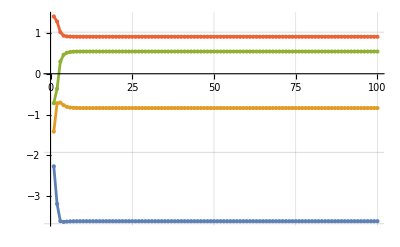

```mathematica
ListPlot[Map[Sort,Map[Diagonal,Data]]ᵀ,Joined->True,Mesh->All,
GridLines->{Automatic,Eigenvalues[A0]}]
```

```mathematica
A=A0;
Table[
α=Diagonal[A];
B = BDiaS[α,A];
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A=Q.A.Qᵀ,
{10}]
```

{{{1.60539,-0.250412,-0.20597,0.258118},{-0.250412,-1.78557,-0.252202,0.182212},{-0.20597,-0.252202,-1.19001,-0.250767},{0.258118,0.182212,-0.250767,1.4561}},{{1.77201,-0.212817,-0.210262,0.122348},{-0.212817,-1.88319,0.0306707,0.181317},{-0.210262,0.0306707,-1.09175,-0.272723},{0.122348,0.181317,-0.272723,1.28884}},{{1.78549,-0.187774,-0.207356,0.0993898},{-0.187774,-1.88113,0.0606762,0.187204},{-0.207356,0.0606762,-1.0928,-0.288311},{0.0993898,0.187204,-0.288311,1.27435}},{{1.78654,-0.186591,-0.206466,0.0975668},{-0.186591,-1.88063,0.0632598,0.188328},{-0.206466,0.0632598,-1.09326,-0.289021},{0.0975668,0.188328,-0.289021,1.27325}},{{1.78663,-0.186533,-0.206373,0.0974069},{-0.186533,-1.88057,0.0634996,0.188439},{-0.206373,0.0634996,-1.09331,-0.289054},{0.0974069,0.188439,-0.289054,1.27316}},{{1.78664,-0.18653,-0.206364,0.0973925},{-0.18653,-1.88057,0.0635216,0.188449},{-0.206364,0.0635216,-1.09332,-0.289056},{0.0973925,0.188449,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.0973912},{-0.186529,-1.88057,0.0635236,0.18845},{-0.206364,0.0635236,-1.09332,-0.289056},{0.0973912,0.18845,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.097391},{-0.186529,-1.88057,0.0635238,0.18845},{-0.206364,0.0635238,-1.09332,-0.289056},{0.097391,0.18845,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.097391},{-0.186529,-1.88057,0.0635238,0.18845},{-0.206364,0.0635238,-1.09332,-0.289056},{0.097391,0.18845,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.097391},{-0.186529,-1.88057,0.0635238,0.18845},{-0.206364,0.0635238,-1.09332,-0.289056},{0.097391,0.18845,-0.289056,1.27315}}}